```mathematica
Clear[a,b]
Num = 3;
f[x_]:= x^(2-a)*1/(1+x)^(b-a)
s[t_, n_]:=Normal[Series[f[x], {x, 2^n, Num}]]/.x->t
```

```mathematica
s[0.000002]
```

0.0000275945

```mathematica
g[r_]:= Integrate[s[x], {x, 0 , r}]
```

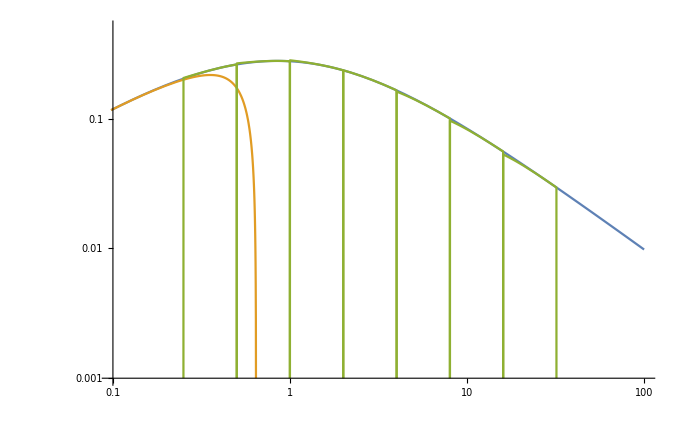

```mathematica
LogLogPlot[{f[r],s0[r], Table[s[r, n] * If[2^(n-1) < r < 2^n, 1, 10^-10], {n, -1, 5}]}, {r, 0, 100}, PlotRange->{{.1, 100},{0.001, 0.5}}]
```

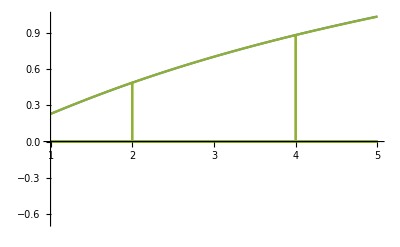

```mathematica
Plot[{Integrate[f[t], {t, 0, r}],s0[r], Table[(Integrate[s[x, n],{x,2^(n-1), r}]  + Integrate[f[t], {t, 0, 2^(n-1)}])* If[2^(n-1) < r < 2^n, 1, 10^-10], {n, -1, 5}]}, {r, 1, 5}]
```

```mathematica
s0[x]
```

x^-a (x^2+(a-b) x^3+1/2 (-1+a-b) (a-b) x^4)

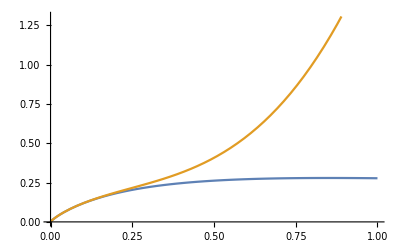

```mathematica
Plot[{f[x], x^-a(x^2+(a-b)x^3 + 1/2 (a-b-1)(a-b)x^4) }, {x, 0 ,1}]
```

```mathematica
d
```

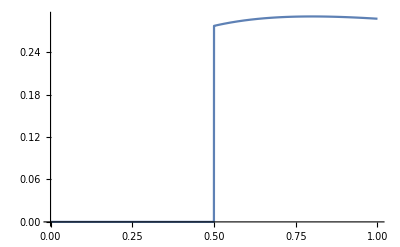

```mathematica
Plot[Table[s[r, n] * If[2^(n-1) < r < 2^(n+1), 1, 0], {n, 0, 5}][[1]], {r, 0, 1}]
```

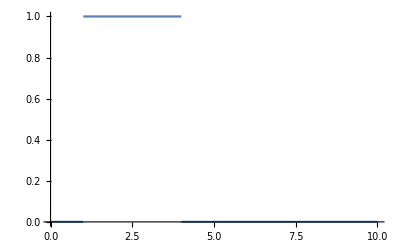

```mathematica
Plot[If[2^(n-1) < r < 2^(n+1), 1, 0], {r, 0, 10}]
```

```mathematica
s25[x]
```

```mathematica
s[x, 5]
```

32^(2-a) 33^(a-b)-32^(1-a) 33^(-1+a-b) (-66+a+32 b) (-32+x)+2^(-1-5 a) 33^(-2+a-b) (2178-67 a+a^2-3200 b+64 a b+1024 b^2) (-32+x)^2-2^(-6-5 a) 3^(-4+a-b) 11^(-3+a-b) (2 a-3 a^2+a^3+71872 b-3360 a b+96 a^2 b-104448 b^2+3072 a b^2+32768 b^3) (-32+x)^3

```mathematica
s0[x]
```

x^-a (x^2+(a-b) x^3)

```mathematica
p = 5;
CForm[Integrate[s[x, p+1],{x,2^p, r}] //Simplify]
```

(Power(2,-7 - 6*a)*Power(65,-3 + a - b)*
     (-13822328832000 + 431947776000*r - 
       (((-2 + a)*(-1 + a)*a + 64*(8582 + 3*(-67 + a)*a)*b + 
            12288*(-66 + a)*Power(b,2) + 262144*Power(b,3))*(-96 + r)*(-32 + r)*
          (5120 + (-128 + r)*r))/4. - 
       51916800*(-130 + a + 64*b)*(3072 - 128*r + Power(r,2)) + 
       4160*(8450 + Power(a,2) - 12544*b + 4096*Power(b,2) + a*(-131 + 128*b))*
        (-229376 + r*(12288 + (-192 + r)*r))))/3.

(Power(4,-2 + b)*Power(5,-3 + a - b)*(-187.5 - ((64*Power(a,3) + 48*Power(a,2)*(-4 + b) + b*(122 - 27*b + Power(b,2)) + 4*a*(32 - 39*b + 3*Power(b,2)))*
          (-1 + Power(1 - 4*r,4)))/32. + 375*r - 75*(-10 + 4*a + b)*r*(-1 + 2*r) + 
       (5*(50 + 16*Power(a,2) + 8*a*(-7 + b) - 19*b + Power(b,2))*(-1 + 6*r - 24*Power(r,2) + 32*Power(r,3)))/4.))/3.

```mathematica
alpha = 1.35760;
beta = 3;
```

```mathematica
Integrate[x^(2-alpha) (1+x)^(alpha-beta), {x, 0, 7.693701}]
```

1.49824